# © Kamal K. Barley, Andreas Ruffing, and Sergei K. Suslov “Oganesson versus Uranium Hydrogen-like Ions from the Viewpoint of Old Quantum Mechanics”

arXiv:2509.06249v2[quant-ph] 11 Sept 2025

https://arxiv.org/pdf/2509.06249

(Last modified/executed on September  21, 2025;  4:45 AM Arizona time.)

```mathematica
SetDirectory[NotebookDirectory[]];
```

0.337408

0.967653

0.0169559

{0.000548474,0.0333634}

12.3387

18.6219

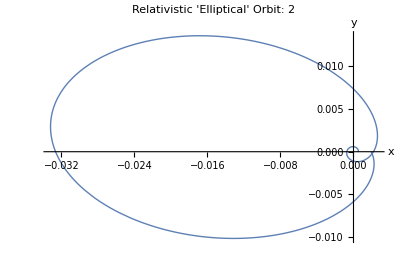

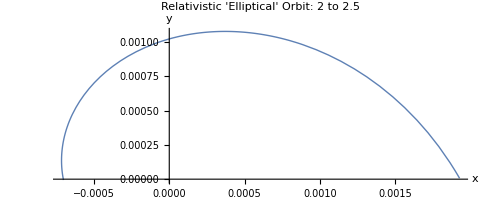

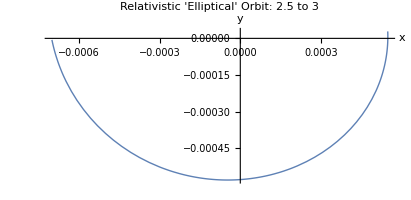

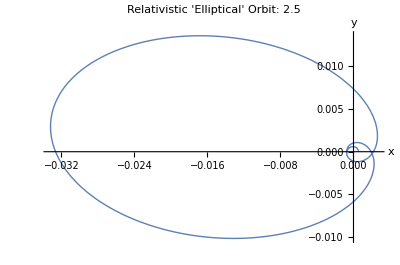

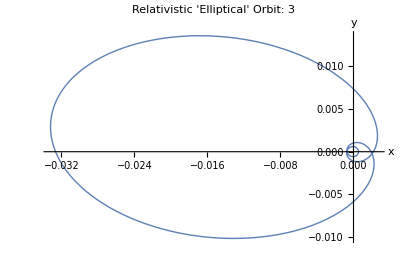

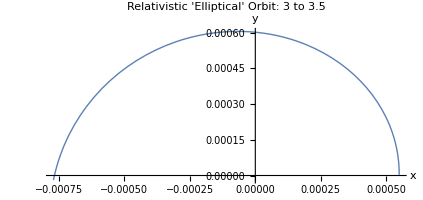

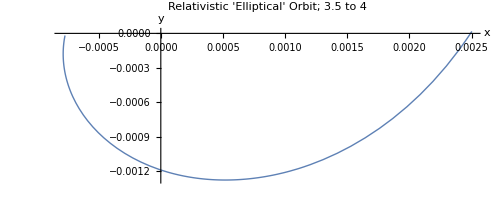

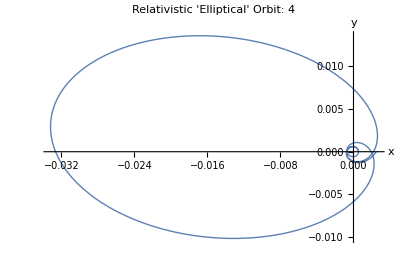

```mathematica
(*---Constants and Setup---*)(*Pretty print subscript-style variables for display only*)MakeBoxes[nt,StandardForm]:=SubscriptBox["n","t"]
MakeBoxes[nr,StandardForm]:=SubscriptBox["n","r"]

(*Physical constants*)
Z=129; (*Atomic number number 129 is assigned for a hypothetical undiscovered element temporarily named Unbiennium, Ube*)

α=1/137.036; (*Fine structure constant*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Define symbolic formulas as functions---*)

(*Eq.(3.19)*)
ωFunc[nt_]:=Sqrt[nt^2-Z^2 α^2]/nt

(*Eq.(3.20)*)
ϵFunc[nt_,nr_]:=Sqrt[nr] Sqrt[(nr+2 Sqrt[nt^2-Z^2 α^2])]/(nr+Sqrt[nt^2-Z^2 α^2])

(*Eq.(3.21)*)
aFunc[nt_,nr_]:=((nr+Sqrt[nt^2-Z^2 α^2]) Sqrt[Z^2 α^2+(nr+Sqrt[nt^2-Z^2 α^2])^2])/Z

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.675*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.675*PeriodTheta, 0.844*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 to 2.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.844*PeriodTheta, 1.015*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5 to 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.844*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.0125*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,1.0125*PeriodTheta,1.18225*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3 to 3.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,1.182225*PeriodTheta, 1.35*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit; 3.5 to 4",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0, 1.35*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0, 1.5*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Export["UnbienniumIon128.pdf",]
```

UnbienniumIon128.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,24 Pi,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in a hypothetical hydrogen-like ion of Unbiseptium, Ube, when Z=129, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.425684,  ϵ=0.954384, and a=0.0194146, in Bohr’s atomic units. The ‘winding number’ is 4.
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.000885619 and r_max=a (1+ϵ)=0.03794357591, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=8.47701.